# I use this notebook to check on Hasting’s 2002 results

```mathematica
(*1. Clear any old tasks from memory first*)
If[ValueQ[autoSaveTask],TaskRemove[autoSaveTask]];

(*2. Capture the exact notebook handle right now*)
thisNotebook=EvaluationNotebook[];

(*3. Start the background task (Set to 5 seconds for a quick test)*)
autoSaveTask=SessionSubmit[ScheduledTask[NotebookSave[thisNotebook];
(*Optional:Flash a quick status message in the window's bottom left bar*)CurrentValue[thisNotebook,WindowStatusArea]="Auto-saved: "<>DateString["Time"],180]];

FS=FullSimplify;
```

## Intro

KEY: THIS IS THE MULTIFRACTAL SPECTRUM OF THE HARMONIC MEASURE!!

The physical multifractal spectrum τ(q) is related to the one in mathematical space τ_y(q) through the relation

There are two expressions for τ_y(q): one around the growing tip and another one away from it

where

```mathematica
$Assumptions=m>0
```

m>0

## § d_f=(τ(q))/(q-1)|_(q=0) ? YESS

```mathematica
ClearAll[τtip,τbulk]
τtip[q_]:=2q-m-1+Sqrt[(m+1)^2-2m q]
τbulk[q_]:=2q-m-1+Sqrt[(m+1)^2-2m q]-(m+1-Sqrt[(m+1)^2-2m q])/m-1
```

Let’s invert the relation around q=0

```mathematica
τ=a0 + a1 q 

Normal@Series[-τtip[-τ],{q,0,1}]
equasTip={(%/.q->0)==0, 
		(D[%,q]/.q->0)== 1}

Normal@Series[-τbulk[-τ],{q,0,1}]
equasBulk={(%/.q->0)==0, 
		(D[%,q]/.q->0)== 1}
```

a0+a1 q

1+2 a0+m-√(1+2 m+2 a0 m+m^2)+(2 a1-(a1 m)/(√(1+2 m+2 a0 m+m^2))) q

{1+2 a0+m-√(1+2 m+2 a0 m+m^2)==0,2 a1-(a1 m)/(√(1+2 m+2 a0 m+m^2))==1}

2+2 a0+m-√(1+2 m+2 a0 m+m^2)+(1+m-√(1+2 m+2 a0 m+m^2))/m+(2 a1-a1/(√(1+2 m+2 a0 m+m^2))-(a1 m)/(√(1+2 m+2 a0 m+m^2))) q

{2+2 a0+m-√(1+2 m+2 a0 m+m^2)+(1+m-√(1+2 m+2 a0 m+m^2))/m==0,2 a1-a1/(√(1+2 m+2 a0 m+m^2))-(a1 m)/(√(1+2 m+2 a0 m+m^2))==1}

Tip

```mathematica
Solve[equasTip,{a0,a1},Reals]//FS
τ/.%//FS
Limit[%/(q-1),q->0]//Expand
```

{{a0→0,a1→(1+m)/(2+m)}}

{((1+m) q)/(2+m)}

{0}

Bulk

```mathematica
Solve[equasBulk,{a0,a1},Reals]//FS
τ/.%//FS
Limit[%/(q-1),q->0]//Expand
```

{{a0→ConditionalExpression[-1-m/2, m≠1],a1→ConditionalExpression[1/(1-m), m≠1]},{a0→ConditionalExpression[-1-1/(2 m), m≠1],a1→ConditionalExpression[m/(-1+m), m≠1]}}

{ConditionalExpression[-1-m/2+q/(1-m), m≠1],ConditionalExpression[-1-1/(2 m)+(m q)/(-1+m), m≠1]}

{1+m/2,1+1/(2 m)}

```mathematica
(*This is correct! It symmetric under m<->1/m*)
```

## § Is it always (i.e. for all b) multifractal?

```mathematica
ClearAll[τtip,τbulk]
τtip[q_]:=2q-m-1+Sqrt[(m+1)^2-2m q]
τbulk[q_]:=2q-m-1+Sqrt[(m+1)^2-2m q]-(m+1-Sqrt[(m+1)^2-2m q])/m-1
```

### Let’s invert the relation around q=1 ANALYTICALLY

I’m not sure I can do it analytically.
Can I expand τ(q) around q0 and look for the coefficients that solve

First way

```mathematica
q0=1

τ=a0 + a1 (q-q0)

Normal@Series[-τtip[-τ],{q,q0,1}]/.q-q0->x
equasTip={(%/.x->0)==q0, 
		(D[%,x]/.x->0)== 1}

Normal@Series[-τbulk[-τ],{q,q0,1}]/.q-q0->x
equasBulk={(%/.x->0)==q0, 
		(D[%,x]/.x->0)== 1}
```

1

a0+a1 (-1+q)

1+2 a0+m-√(1+2 m+2 a0 m+m^2)+(2 a1-(a1 m)/(√(1+2 m+2 a0 m+m^2))) x

{1+2 a0+m-√(1+2 m+2 a0 m+m^2)==1,2 a1-(a1 m)/(√(1+2 m+2 a0 m+m^2))==1}

2+2 a0+m-√(1+2 m+2 a0 m+m^2)+(1+m-√(1+2 m+2 a0 m+m^2))/m+(2 a1-a1/(√(1+2 m+2 a0 m+m^2))-(a1 m)/(√(1+2 m+2 a0 m+m^2))) x

{2+2 a0+m-√(1+2 m+2 a0 m+m^2)+(1+m-√(1+2 m+2 a0 m+m^2))/m==1,2 a1-a1/(√(1+2 m+2 a0 m+m^2))-(a1 m)/(√(1+2 m+2 a0 m+m^2))==1}

Tip

```mathematica
Solve[equasTip,{a0,a1},Reals]//FS
τ/.%//FS
Limit[%/(q-1),q->q0]//Expand
```

{{a0→1/4 (-m+√(4+m (8+m))),a1→1/(2-(√2 m)/(√(2+m (4+m+√(4+m (8+m))))))}}

{1/4 (-m+√(4+m (8+m)))+(-1+q)/(2-(√2 m)/(√(2+m (4+m+√(4+m (8+m))))))}

{Indeterminate}

Bulk

```mathematica
Solve[equasBulk,{a0,a1},Reals]//FS
τ/.%//FS
Limit[%/(q-1),q->q0]//Expand
```

{{a0→0,a1→1}}

{-1+q}

{1}

```mathematica
(*This is the expected result for the Information exponent of the multifractal HARMONIC measure *)
```

Second way (which should be manifestly wrong: I truncate τ to first order in (q - q0), but then I expand it to first order in q ti match the rhs. This should be wrong because there are infinite contributions from the first order in q of (q - q0)^n. However I get the same result...)

```mathematica
q0=1

τ=a0 + a1 (q-q0)

Normal@Series[-τtip[-τ],{q,q0,1}]//Expand
equasTip={(%/.q->0)==0, 
		(D[%,q]/.q->0)== 1}

Normal@Series[-τbulk[-τ],{q,q0,1}]//Expand
equasBulk={(%/.q->0)==0, 
		(D[%,q]/.q->0)== 1}
```

1

a0+a1 (-1+q)

1+2 a0-2 a1+m+(a1 m)/(√(1+2 m+2 a0 m+m^2))-√(1+2 m+2 a0 m+m^2)+2 a1 q-(a1 m q)/(√(1+2 m+2 a0 m+m^2))

{1+2 a0-2 a1+m+(a1 m)/(√(1+2 m+2 a0 m+m^2))-√(1+2 m+2 a0 m+m^2)==0,2 a1-(a1 m)/(√(1+2 m+2 a0 m+m^2))==1}

3+2 a0-2 a1+1/m+m+a1/(√(1+2 m+2 a0 m+m^2))+(a1 m)/(√(1+2 m+2 a0 m+m^2))-√(1+2 m+2 a0 m+m^2)-(√(1+2 m+2 a0 m+m^2))/m+2 a1 q-(a1 q)/(√(1+2 m+2 a0 m+m^2))-(a1 m q)/(√(1+2 m+2 a0 m+m^2))

{3+2 a0-2 a1+1/m+m+a1/(√(1+2 m+2 a0 m+m^2))+(a1 m)/(√(1+2 m+2 a0 m+m^2))-√(1+2 m+2 a0 m+m^2)-(√(1+2 m+2 a0 m+m^2))/m==0,2 a1-a1/(√(1+2 m+2 a0 m+m^2))-(a1 m)/(√(1+2 m+2 a0 m+m^2))==1}

Tip

```mathematica
Solve[equasTip,{a0,a1},Reals]//FS
τ/.%//FS
Limit[%/(q-1),q->q0]//Expand
```

{{a0→1/4 (-m+√(4+m (8+m))),a1→(√(2+m (4+m+√(4+m (8+m)))) (2+m+√(4+m (8+m))-√(4+2 m (4+m+√(4+m (8+m))))))/(-2 √2 m+4 √(2+m (4+m+√(4+m (8+m)))))}}

{1/4 (-m+√(4+m (8+m)))+(√(2+m (4+m+√(4+m (8+m)))) (2+m+√(4+m (8+m))-√(4+2 m (4+m+√(4+m (8+m))))) (-1+q))/(-2 √2 m+4 √(2+m (4+m+√(4+m (8+m)))))}

{Indeterminate}

Bulk

```mathematica
Solve[equasBulk,{a0,a1},Reals]//FS;
τ/.%//FS;
Limit[%/(q-1),q->q0]//Expand
```

{1}

### Let’s invert the relation around q={1,2,3,...} ANALYTICALLY

```mathematica
multifractalDims=Table[
τ=a0 + a1 (q-q0);

serTip=Normal@Series[-τtip[-τ],{q,q0,1}]/.q-q0->x;
equasTip={(serTip/.x->0)==q0, 
		(D[serTip,x]/.x->0)== 1};

serBulk=Normal@Series[-τbulk[-τ],{q,q0,1}]/.q-q0->x;
equasBulk={(serBulk/.x->0)==q0, 
		(D[serBulk,x]/.x->0)== 1};

solTip=Solve[equasTip,{a0,a1},Reals]//FS;
solBulk=Solve[equasBulk,{a0,a1},Reals]//FS;

{Row[{"q0=",q0}],Limit[(τ/.solTip)/(q-1),q->q0]//Expand,
Limit[(τ/.solBulk)/(q-1),q->q0]//Expand}

,{q0,0,3}]
```

{{q0=0,{0},{1+m/2,1+1/(2 m)}},{q0=1,{Indeterminate},{1}},{q0=2,{1/2-m/4+1/4 √(4+m (12+m))},{-1/(4 m)-m/4+1/4 √(1+m (6+m))+(√(1+m (6+m)))/(4 m)}},{q0=3,{1/2-m/8+1/8 √(4+m (16+m))},{1/4-1/(8 m)-m/8+1/8 √(1+m (10+m))+(√(1+m (10+m)))/(8 m)}}}

```mathematica
multifractalDims={{"q0="0,{0},{1+m/2,1+1/(2 m)}},{"q0="1,{Indeterminate},{1}},{"q0="2,{1/2-m/4+1/4 √(4+m (12+m))},{-1/(4 m)-m/4+1/4 √(1+m (6+m))+(√(1+m (6+m)))/(4 m)}},{"q0="3,{1/2-m/8+1/8 √(4+m (16+m))},{1/4-1/(8 m)-m/8+1/8 √(1+m (10+m))+(√(1+m (10+m)))/(8 m)}}}
```

{{q0=0,{0},{1+m/2,1+1/(2 m)}},{q0=1,{Indeterminate},{1}},{q0=2,{1/2-m/4+1/4 √(4+m (12+m))},{-1/(4 m)-m/4+1/4 √(1+m (6+m))+(√(1+m (6+m)))/(4 m)}},{q0=3,{1/2-m/8+1/8 √(4+m (16+m))},{1/4-1/(8 m)-m/8+1/8 √(1+m (10+m))+(√(1+m (10+m)))/(8 m)}}}

Check for LRW=LERW i.e. m=1/2 (I know this is a simple fractal, no??)

```mathematica
multifractalDims[[All,3,1]]/.m->1/2 //N
```

{1.25,1.,0.921165,0.875}

```mathematica
(*Multifractal??*)
```

### Numerical inversion for m=1/2 (i.e. LERW=LRW)

```mathematica
ClearAll[τtip1,τbulk1]
τtip[q]/.m->1/2
τtip1[q_]:=-3/2+√(9/4-q)+2 q

τbulk[q]/.m->1/2
τbulk1[q_]:=-5/2-2 (3/2-√(9/4-q))+√(9/4-q)+2 q
```

-3/2+√(9/4-q)+2 q

-5/2-2 (3/2-√(9/4-q))+√(9/4-q)+2 q

```mathematica
τtip1[q]
τbulk1[q]
```

-3/2+√(9/4-q)+2 q

-5/2-2 (3/2-√(9/4-q))+√(9/4-q)+2 q

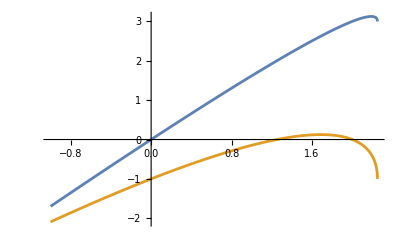

```mathematica
Plot[{τtip1[q]
,τbulk1[q]},{q,-1,9/4}]
```

```mathematica
With[{q=0.2},
Solve[τbulk1[qsol]==q,qsol]
]
```

{{qsol→1.725-0.290474 ⅈ},{qsol→1.725+0.290474 ⅈ}}

```mathematica
τData=Flatten@Table[
Solve[τbulk1[qsol]==q,qsol,Reals]
,{q,0,3}]
```

{qsol→5/4,qsol→2}

### Numerical inversion general case

Plots of  τtip[q] and τbulk[q]

```mathematica
τtip[q]
τbulk[q]
```

-1-m+2 q+√((1+m)^2-2 m q)

-2-m+2 q+√((1+m)^2-2 m q)-(1+m-√((1+m)^2-2 m q))/m

```mathematica
Manipulate[
Plot[{τtip[q]/.m->mm,τbulk[q]/.m->mm},{q,-1,(1+mm)^2/(2mm)},PlotRange->{{-1,All},{-2,3}},Exclusions->{q==1},PlotLegends->{"τtip","τbulk"}]
,{mm,0.1,30.,0.1}]
```

```mathematica
(*τbulk is always below τtip, i.e. it's always the mininum and hence the real multifractal spectrum*)
```

```mathematica
Manipulate[
Plot[{(*τtip[q]/(q-1)/.m->mm,*)τbulk[q]/(q-1)/.m->mm},{q,0,(1+mm)^2/(2mm)},PlotRange->{All,{-1,2}},Exclusions->{q==1},PlotLegends->{(*"τtip/(q - 1)",*)"τbulk/(q - 1)"}]
,{mm,0.1,30.,0.1}]
```

Numerical inversion just using τbulk[q] (the real multifractal spectrum)

These are the spectra in mathematical space, so to get those in real space one should invert the relation

```mathematica
τRealSpace[q_]:=Quiet@SolveValues[-τbulk[-τdata]==q,τdata,Reals]
```

```mathematica
τRealSpace[0]
First[%]==(Last[%]/.m->1/m)
%/.m->0.5
```

{ConditionalExpression[1/2 (-2-m), m>1||m<1],ConditionalExpression[(-1-2 m)/(2 m), m>1||m<1]}

ConditionalExpression[1/2 (-2-m)==1/2 (-1-2/m) m, (m>1||m<1)&&(0<m<1||m>1||m<0)]

True

```mathematica
Manipulate[
Plot[{Max[τRealSpace[q]/.m->mm]},{q,0,(1+mm)^2/(2mm)},PlotRange->All,Exclusions->{0<q<1},PlotLegends->Row[{"m = ",mm,"\nb = ", (3-2mm)/(4 mm)}],AxesLabel->{"q","τRealSpace"}]
,{mm,0.1,30.,0.1}]
```

```mathematica
Manipulate[
Plot[{τRealSpace[q]/(q-1)/.m->mm},{q,0,10(*(1+mm)^2/(2mm)*)},PlotRange->{{0,All},{0,2}},Exclusions->{q==1},
PlotLegends->Row[{"m = ",mm,"\nb = ", (3-2mm)/(4 mm)}],AxesLabel->{"q","τRealSpace/(q - 1)"}]
,{mm,0.1,30.,0.1}]
```

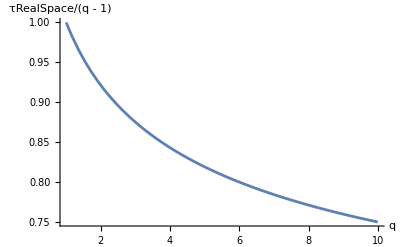

```mathematica
With[{mm=0.5},
Plot[{τRealSpace[q]/(q-1)/.m->mm},{q,1,10(*(1+mm)^2/(2mm)*)},PlotRange->{{0,All},{0,2}},Exclusions->{q==1},
PlotLegends->Row[{"m = ",mm,"\nb = ", (3-2mm)/(4 mm)}],AxesLabel->{"q","τRealSpace/(q - 1)"}]
]
```